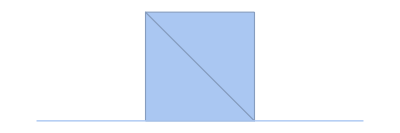

```mathematica
(*The shape we are solving over*)
newShape = MeshRegion[{{0,0},{1,0},{2,0},{3,0},{1,1},{2,1}},{Line[{1,4}],Simplex[{2,3,5}],Simplex[{3,5,6}]}]
```

```mathematica
Manipulate[Plot[{-k*x*(x-3),10},{x,0,3}],{k,-20,20}]
```

```mathematica
(*Based on above, I will make the following the IC for the rod*)
ff[x_]:= -5*x*(x-3)
```

```mathematica
alpha1 = 0.05; 
uvals = NDSolveValue[{{D[u[x,t],t]==alpha1*D[u[x,t],{x,2}]},{u[x,0]==ff[x]},{u[0,t]==0},{u[3,t]==0}},u,{x,0,3},{t,0,20}]
```

InterpolatingFunction[{{0., 3.}, {0., 20.}}, <>]

```mathematica
Manipulate[Plot[{uvals[x,t],12},{x,0,3}],{t,0,20}]
```

```mathematica
alpha3 = 0.05;
vvals = NDSolveValue[{{D[v[x,y,t],t]==alpha3*(D[v[x,y,t],{x,2}]+D[v[x,y,t],{y,2}])},{v[x,y,0]==ff[x]},{v[x,0,t]==uvals[x,t]}},v,{x,1,2},{y,1,2},{t,0,20}]
```

NDSolveValue::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

NDSolveValue::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

InterpolatingFunction[{{1., 2.}, {0., 2.}, {0., 20.}}, <>]

```mathematica
Manipulate[Plot3D[{vvals[x,y,t],12},{x,1,2},{y,1,2}],{t,0,20}]
```

```mathematica
vvals2 = NDSolveValue[{{D[v[x,y,t],t]==alpha3*(D[v[x,y,t],{x,2}]+D[v[x,y,t],{y,2}])},{v[x,y,0]==ff[x]*(1-y)},{v[x,0,t]==uvals[x,t]}},v,{x,1,2},{y,0,1},{t,0,20}]
```

NDSolveValue::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

NDSolveValue::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

InterpolatingFunction[{{1., 2.}, {0., 1.}, {0., 20.}}, <>]

```mathematica
Manipulate[Plot3D[{vvals2[x,y,t],12},{x,1,2},{y,1,2}],{t,0,20}]
```

InterpolatingFunction::dmval: Input value {1.00007,1.00007,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.00007,1.00007,13.6} lies outside the range of data in the interpolating function. Extrapolation will be used.

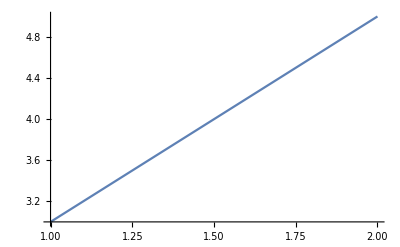

```mathematica
Plot[3*(2-x)+5*(x-1),{x,1,2}]
```

```mathematica
vvals3 = NDSolveValue[{{D[v[x,y,t],t]==alpha3*(D[v[x,y,t],{x,2}]+D[v[x,y,t],{y,2}])},{v[x,y,0]==ff[x]},{v[x,0,t]==uvals[x,t]},{v[1,y,t]==uvals[1,t]},{v[2,y,t]==uvals[2,t]},{v[x,1,t]==uvals[1,t]*(2-x)+uvals[2,t]*(x-1)}},v,{x,1,2},{y,0,1},{t,0,20}]
```

NDSolveValue::ibcinc: Warning: boundary and initial conditions are inconsistent.

InterpolatingFunction[{{1., 2.}, {0., 1.}, {0., 20.}}, <>]

```mathematica
Manipulate[Plot3D[{vvals3[x,y,t],12},{x,1,2},{y,0,1}],{t,0,20}]
```